# FIGURE for Paper: Representation theory for Gaussian unitary transformations

## Figure 4a: Example - 4 bosons

### Bosonic generator

```mathematica
II=0 IdentityMatrix[4];
IR=({{0, 0, 0, ν}, {0, 0, ν, 1}, {0, ν, -1, 0}, {ν, 1, 0, 0}});
IL=({{0, 0, -1, -ν}, {0, 1, -ν, 0}, {-1, -ν, 0, 0}, {-ν, 0, 0, 0}});
K=ArrayFlatten[({{II, IR}, {IL, -Transpose[II]}})];
KN=K/.ν-> 0;
KI=K-KN;
```

### Random change of basis

```mathematica
J0=ArrayFlatten[({{0, IdentityMatrix[4]}, {-IdentityMatrix[4], 0}})];
Ω=J0;
A=RandomReal[{-1,1},{8,8}];
Kran=Ω.(A+Transpose[A]);
TT=MatrixExp[Kran];
J=TT.J0.Inverse[TT];
rule={μ-> RandomReal[{-1,1}],ν-> RandomReal[{-1,1}]};
rule=ν-> 0;
K=2({{0, 0, 0, 0, ν1, 0, 0, 0}, {0, 0, 0, 0, 0, ν2, 0, 0}, {0, 0, 0, 0, 0, 0, ν3, 0}, {0, 0, 0, 0, 0, 0, 0, 1}, {-ν1, 0, 0, 0, 0, 0, 0, 0}, {0, -ν2, 0, 0, 0, 0, 0, 0}, {0, 0, -ν3, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}})/.{ ν1-> RandomReal[{-1,1}],ν2-> RandomReal[{-1,1}],ν3-> RandomReal[{-1,1}]};
KN=2({{0, 0, 0, 0, ν1, 0, 0, 0}, {0, 0, 0, 0, 0, ν2, 0, 0}, {0, 0, 0, 0, 0, 0, ν3, 0}, {0, 0, 0, 0, 0, 0, 0, 1}, {-ν1, 0, 0, 0, 0, 0, 0, 0}, {0, -ν2, 0, 0, 0, 0, 0, 0}, {0, 0, -ν3, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}})/.{ ν1-> 0,ν2->0,ν3->0};
KI=K-KN;
KK=TT.K.Inverse[TT];
KKI=TT.KI.Inverse[TT];
KKN=TT.KN.Inverse[TT];
```

### Using cocycle formalism

```mathematica
det0[z_]:=Det[z⟦1;;4,1;;4⟧+ⅈ z⟦1;;4,5;;8⟧];
tr0[z_]:=Tr[z⟦1;;4,1;;4⟧+ⅈ z⟦1;;4,5;;8⟧];

Cg0[g_]:=(g-J0.g.J0)/2;
Dg0[g_]:=(g+J0.g.J0)/2;

Zg0[g_]:=Inverse[Cg0[g]].Dg0[g];
ZgI0[g_]:=-Cg0[g].Zg0[g].Inverse[Cg0[g]];

φ0[g_]:=Arg[det0[Cg0[g]]];
absφ0[g_]:=Abs[det0[Cg0[g]]];

con[z_]:=z⟦1;;4,1;;4⟧+ⅈ z⟦1;;4,5;;8⟧;
η00[g1_,g2_]:=Arg/@Eigenvalues[con[IdentityMatrix[8]-Zg0[g1].ZgI0[g2]]]//Total;

M[t_]:=MatrixExp[t KK];
MN[t_]:=MatrixExp[t KKN];
```

```mathematica
Tr[KKI.J]
Tr[KI.J]
```

-3.29381

-155.645

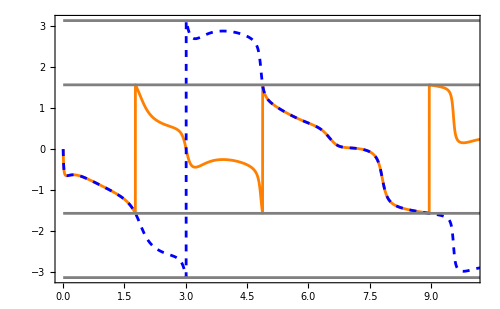

```mathematica
length=10;
P=Show[Plot[{-φ0[M[t]]/2,Arg[Exp[ⅈ t Tr[KKI.J]/4+ⅈ (η00[Inverse[TT],MatrixExp[t KK]]+η00[Inverse[TT].MatrixExp[t KK],TT]-Sum[Arg[λ],{λ,Eigenvalues[con[Cg0[Inverse[TT].MN[t].TT]]]}])/2]]},{t,0,40},Exclusions->None,PlotStyle->{Orange,{Blue,Dashed}},Frame->True,PlotRange->{{0,length},{-π,π}},PlotPoints->400,ImageSize->500],Plot[{π,-π,π/2,-π/2},{x,0,40},PlotStyle->{Gray}]]
Export[NotebookDirectory[]<>"figure4a.pdf",P];
```

```mathematica
Show[Plot[{-φ0[M[t]]/2,Arg[Exp[ⅈ t Tr[KKI.J]+ⅈ (η00[Inverse[TT],MatrixExp[t KK]]+η00[Inverse[TT].MatrixExp[t KK],TT]-Sum[Arg[λ],{λ,Eigenvalues[con[Cg0[Inverse[TT].M[t].TT]]]}])/2]],0Arg[Exp[-ⅈ t Tr[KKI.J]+ⅈ (Sum[Arg[λ],{λ,Eigenvalues[con[Cg0[MN[t]]]]}])/2]]},{t,0,40},Exclusions->None,PlotStyle->{Black,{Red,Dashed},{Green,Dotted}},PlotRange->All],Plot[{π,-π,π/2,-π/2},{x,0,40},PlotStyle->{Gray}]];
```

## Figure 4b: Example - 4 fermions

```mathematica
fontsize=14;
SetOptions[{Plot,ListPlot,ArrayPlot,ContourPlot,ComplexPlot},BaseStyle->{12,Directive[FontFamily->"LM Roman 12"]}];
```

### Creating the matrix representation

```mathematica
T=4;
σp=({{0, 1}, {0, 0}});
σm=({{0, 0}, {1, 0}});
σ3=({{1, 0}, {0, -1}});
Id=IdentityMatrix[2];
A1d=TensorProduct[σm,Id,Id,Id]//Flatten[#,{{1,3,5,7},{2,4,6,8}}]&;
A1=TensorProduct[σp,Id,Id,Id]//Flatten[#,{{1,3,5,7},{2,4,6,8}}]&;
A2d=TensorProduct[σ3,σm,Id,Id]//Flatten[#,{{1,3,5,7},{2,4,6,8}}]&;
A2=TensorProduct[σ3,σp,Id,Id]//Flatten[#,{{1,3,5,7},{2,4,6,8}}]&;
A3d=TensorProduct[σ3,σ3,σm,Id]//Flatten[#,{{1,3,5,7},{2,4,6,8}}]&;
A3=TensorProduct[σ3,σ3,σp,Id]//Flatten[#,{{1,3,5,7},{2,4,6,8}}]&;
A4d=TensorProduct[σ3,σ3,σ3,σm]//Flatten[#,{{1,3,5,7},{2,4,6,8}}]&;
A4=TensorProduct[σ3,σ3,σ3,σp]//Flatten[#,{{1,3,5,7},{2,4,6,8}}]&;

ξ=1/(√2){A1d+A1,ⅈ(A1d-A1),A2d+A2,ⅈ(A2d-A2),A3d+A3,ⅈ(A3d-A3),A4d+A4,ⅈ(A4d-A4)};

N1=A1d.A1;N2=A2d.A2;N3=A3d.A3;N4=A4d.A4;
vec=Table[k[N1⟦i,i⟧,N2⟦i,i⟧,N3⟦i,i⟧,N4⟦i,i⟧],{i,16}];vec//MatrixForm
vecT=ArrayReshape[vec,{2,2,2,2}];
vecT⟦1,2,1,2⟧
```

(k[0,0,0,0]
k[0,0,0,1]
k[0,0,1,0]
k[0,0,1,1]
k[0,1,0,0]
k[0,1,0,1]
k[0,1,1,0]
k[0,1,1,1]
k[1,0,0,0]
k[1,0,0,1]
k[1,0,1,0]
k[1,0,1,1]
k[1,1,0,0]
k[1,1,0,1]
k[1,1,1,0]
k[1,1,1,1])

k[0,1,0,1]

### Reference state and its covariance matrix

```mathematica
J0=({{0, 1, 0, 0, 0, 0, 0, 0}, {-1, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0}, {0, 0, -1, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, -1, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 1}, {0, 0, 0, 0, 0, 0, -1, 0}});
```

```mathematica
ψ0=Table[KroneckerDelta[i,1],{i,16}];
Ωψ0=-ⅈ Table[Conjugate[ψ].(x.y-y.x).ψ,{x,ξ},{y,ξ}]//MatrixForm;
```

```mathematica
A=RandomReal[{-1,1},{8,8}];
K=A-Transpose[A];
H=-ⅈ/2 Sum[K⟦i,j⟧ξ⟦i⟧.ξ⟦j⟧,{i,8},{j,8}];
```

```mathematica
{vals,vecs}=Eigensystem[H];
```

```mathematica
ψ=Eigenvectors[H]⟦2⟧//Chop;
Ωψ=-ⅈ Table[Conjugate[ψ].(x.y-y.x).ψ,{x,ξ},{y,ξ}]//Chop;
Ωψ.Ωψ//Chop//MatrixForm
```

(-1. | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1. | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1. | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1. | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1. | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1. | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1. | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.)

```mathematica
Conjugate[ψ].H.ψ
```

3.12659+4.04857×10^-18 ⅈ

```mathematica
J=Ωψ;
```

### Using cocycle formalism

```mathematica
Det[IdentityMatrix[8]+J.J0]
-Tr[J.K]/4
Conjugate[ψ].H.ψ
```

0.669989

3.12659

3.12659+4.04857×10^-18 ⅈ

```mathematica
det0[z_]:=Det[z⟦{1,3,5,7},{1,3,5,7}⟧+ⅈ z⟦{1,3,5,7},{2,4,6,8}⟧];
tr0[z_]:=Tr[z⟦{1,3,5,7},{1,3,5,7}⟧+ⅈ z⟦{1,3,5,7},{2,4,6,8}⟧];

Cg0[g_]:=(g-J0.g.J0)/2;
Dg0[g_]:=(g+J0.g.J0)/2;

Zg0[g_]:=Inverse[Cg0[g]].Dg0[g];
ZgI0[g_]:=-Cg0[g].Zg0[g].Inverse[Cg0[g]];

φ0[g_]:=Arg[det0[Cg0[g]]];
absφ0[g_]:=Abs[det0[Cg0[g]]];

con[z_]:=z⟦{1,3,5,7},{1,3,5,7}⟧+ⅈ z⟦{1,3,5,7},{2,4,6,8}⟧;
η00[g1_,g2_]:=Arg/@Eigenvalues[con[IdentityMatrix[2T]-Zg0[g1].ZgI0[g2]]]//Total;

M[t_]:=MatrixExp[t KK];
Mn[t_]:=MatrixExp[t K];

U[t_]:=MatrixExp[ⅈ t H];
```

```mathematica
Min[Eigenvalues[H]]
Conjugate[ψ].H.ψ
Tr[KK.J0]/4
```

-3.12659

3.12659+4.04857×10^-18 ⅈ

1/4 Tr[KK.{{0,1,0,0,0,0,0,0},{-1,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0},{0,0,-1,0,0,0,0,0},{0,0,0,0,0,1,0,0},{0,0,0,0,-1,0,0,0},{0,0,0,0,0,0,0,1},{0,0,0,0,0,0,-1,0}}]

```mathematica
TT=MatrixPower[-J.J0,1/2];
Inverse[TT].J0.TT-J//Chop;
```

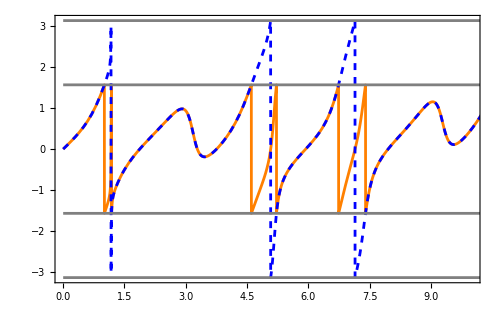

```mathematica
length=10;
P=Show[Plot[{φ0[Mn[t]]/2,Arg[Exp[-ⅈ t Tr[K.J]/4-ⅈ (η00[Inverse[TT],MatrixExp[t K]]+η00[Inverse[TT].MatrixExp[t K],TT])/2]]},{t,0,40},Exclusions->None,PlotStyle->{Orange,{Blue,Dashed}},Frame->True,PlotRange->{{0,length},{-π,π}},PlotPoints->400,ImageSize->500],Plot[{π,-π,π/2,-π/2},{x,0,40},PlotStyle->{Gray}]]
Export[NotebookDirectory[]<>"figure4b.pdf",P];
```

```mathematica
length=10;
Show[Plot[{Arg[Conjugate[ψ0].U[t].ψ0],Arg[Exp[-ⅈ t Tr[K.J]/4-ⅈ (η00[Inverse[TT],MatrixExp[t K]]+η00[Inverse[TT].MatrixExp[t K],TT])/2]],φ0[Mn[t]]/2},{t,0,40},Exclusions->None,PlotStyle->{Black,{Red,Dashed},Blue},Frame->True,PlotRange->{{0,length},{-π,π}}],Plot[{π,-π,π/2,-π/2},{x,0,40},PlotStyle->{Gray}]];
```

```mathematica
Tr[U[.7]]
```

5.3501-5.55112×10^-17 ⅈ

```mathematica
ResourceFunction["Pfaffian"]
```

```mathematica
X=ArrayFlatten[({{√2 MatrixFunction[Sinh,K/4], -IdentityMatrix[8]}, {IdentityMatrix[8], √2 MatrixFunction[Sinh,K/4]}})];
XX=1/2(X-Transpose[X]);
```

MatrixFunction::valtlrg: Warning: at least one value returned by the function or one of its derivatives is significantly larger than its argument. The resulting matrix function may be inaccurate or may not exist.

```mathematica
ResourceFunction["Pfaffian"][XX]
```

0.0352142

## Figure 6: Bosonic case study - 1 boson

```mathematica
R=5π;
fontsize=14;
SetOptions[{Plot,ListPlot,ArrayPlot,ContourPlot,ComplexPlot},BaseStyle->{12,Directive[FontFamily->"LM Roman 12"]}];
Fab[a_,b_]=Cosh[√((a-b) (a+b))]+(ⅈ b Sinh[√((a-b) (a+b))])/(√((a-b) (a+b)));
f[z_]=If[z==0,0,If[Re[z]<Im[z],Exp[-ⅈ(√(b^2-a^2))/2-ⅈ Arg[(1-(a^2 Cosh[2 √(a^2-b^2)])/((b+√(-a^2+b^2))^2)+ⅈ(a^2 Sin[2 √(-a^2+b^2)])/((b+√(-a^2+b^2))^2))]/2]/(√Abs[Cosh[√((a-b) (a+b))]+(ⅈ b Sinh[√((a-b) (a+b))])/(√((a-b) (a+b)))])/.{a-> Re[z],b-> Im[z]},If[Re[z]==Im[z],1/(1+ⅈ Re[z])^(1/2),1/√(Cosh[√((a-b) (a+b))]+(ⅈ b Sinh[√((a-b) (a+b))])/(√((a-b) (a+b))))/.{a-> Re[z],b-> Im[z]}]]];
abs[a_,b_]=If[a==b,1/((1+a^2)^(1/4)),1/((Cosh[√((a-b) (a+b))]^2+((b Sinh[√((a-b) (a+b))])/(√((a-b) (a+b))))^2)^(1/4))];
P1=Show[ComplexPlot[f[z],{z,0,R+R ⅈ},PlotPoints->100,PlotRange->All,PlotPoints->1000,PlotLegends->Automatic,ColorFunction->{Automatic,None},ColorFunctionScaling->True,Frame->True,FrameTicks->{{{0,2π,4π},None},{{0,2π,4π},None}},PlotRangePadding->0,LabelStyle->{FontFamily->"LM Roman 12",FontSize->fontsize}],DensityPlot[Abs[f[a+ⅈ b]],{a,0,R},{b,0,R},Exclusions->None,PlotPoints->100,PlotLegends->Automatic,PlotRange->{0,1},ColorFunction->(Opacity[If[#==.2 ||#==.4||#==.6||#==.8,0,.75-.75Abs[#]],Black]&),LabelStyle->{FontFamily->"LM Roman 12",FontSize->fontsize}],ContourPlot[{abs[a,b]==.8,abs[a,b]==.6,abs[a,b]==.4,abs[a,b]==.2},{a,0,R},{b,0,R},ContourShading->None,Exclusions->None,PlotPoints->200,ContourStyle->{{White,Thickness[.003]}},Exclusions->None]]
Export[NotebookDirectory[]<>"figure6.pdf",P1,ImageResolution->500];
```

-Graphics-

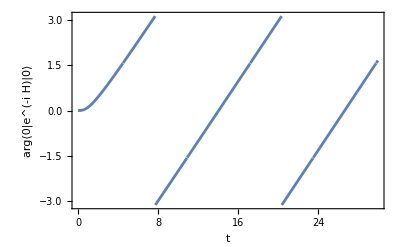

```mathematica
aa=1;
bb=1;
Plot[Arg[f[t(bb+aa ⅈ)] ⅇ^(ⅈ aa t/2)],{t,0,30},Frame->True,FrameLabel->{"t","arg⟨0|e^(-i  H)|0⟩"}]
```

## Figure 8: Fermionic case study - 2 fermions

```mathematica
R=5π;
fontsize=14;
fferm[z_]=Cos[Abs[z]/2]-ⅈ Sin[Abs[z]/2] Im[z]/Abs[z];
absferm[a_,b_]=Abs[Cos[√(a^2+b^2)/2]-ⅈ Sin[√(a^2+b^2)/2] b/(√(a^2+b^2))];
P2=Show[ComplexPlot[fferm[z],{z,0,R+R ⅈ},PlotPoints->100,PlotRange->All,PlotPoints->1000,PlotLegends->Automatic,ColorFunction->{Automatic,None},ColorFunctionScaling->True,Frame->True,FrameTicks->{{{0,2π,4π},None},{{0,2π,4π},None}},PlotRangePadding->0,LabelStyle->{FontFamily->"LM Roman 12",FontSize->fontsize}],DensityPlot[absferm[a,b],{a,0,R},{b,0,R},Exclusions->None,PlotPoints->100,PlotLegends->Automatic,PlotRange->{0,1},ColorFunction->(Opacity[If[#==.2 ||#==.4||#==.6||#==.8,0,1-Abs[#]],Black]&),LabelStyle->{FontFamily->"LM Roman 12",FontSize->fontsize}],ContourPlot[{absferm[a,b]==.8,absferm[a,b]==.6,absferm[a,b]==.4,absferm[a,b]==.2},{a,0,R},{b,0,R},ContourShading->None,Exclusions->None,PlotPoints->200,ContourStyle->{{White,Thickness[.003]}},Exclusions->None]]
Export[NotebookDirectory[]<>"figure8.pdf",P2,ImageResolution->500];
```

-Graphics-